```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

```mathematica
(* Write Module to Count number of roots in a function *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
findNsR[v_,vp_,vpp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_] := Module[{h,hsq,ϕ0,f,ϕi1,ϕpi1,ϕsol1,ϕ1p,h1sq,ϵ1,n1,ϕf2,ϕi2,ϕpi2,ϕsol2,ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Define the hubble parameter *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* Find the slow roll initial conditions *)
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
If[prints,Print["ϕ0 = ",ϕ0]];
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
(* If[prints,Print["f[t] = ",f[t]]]; *)
(*ϕi1= t/.Last[NSolve[ni==f[t],t]];*)
ϕi1= t/.Last[FindRoot[ni-f[t],{t,20}]];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,-nf},AxesLabel->{N,"ϕsol1"},GridLines->{{-1,-1.2},{1}}]]];
(* Find ϵ1 *)
ϕ1p[n_] = D[ϕ[n],n]/.ϕsol1;
h1sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ1p[n]^2)/.ϕsol1;
ϵ1[n_] = Evaluate[Re[3*ϕ1p[n]^2/(ϕ1p[n]^2+2*v[ϕ[n]]/h1sq[n])/.ϕsol1]];
(* ϵ1[n_]:=Chop[Evaluate[1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol1]]; *)
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
(* Find the new initial conditions and re-solve the KG equation *)
(* ϕf2 = ϕ[n1]/.ϕsol1;
ϕi2 = ϕ[ni2]/.ϕsol1; *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
ϕsol2 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni2]==ϕi2,ϕ'[ni2]==ϕpi2(*ϕ[nf2]==ϕf2*)},ϕ,{n,nf2,ni2},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol2],{n,nf2,ni2},AxesLabel->{N,"ϕsol2"}] ]];
(* Find ϵ2 *)
ϕ2p[n_] = D[ϕ[n],n]/.ϕsol2;
h2sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ2p[n]^2)/.ϕsol2;
ϵ2[n_] = Evaluate[3*ϕ2p[n]^2/(ϕ2p[n]^2+2*v[ϕ[n]]/h2sq[n])/.ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,ni2,nf2},AxesLabel->{N,"ns"}]]];
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,10},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,4}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,10},{0,3}}]]];
(* Find Zη and Zϵ, the number of roots of η and ϵ *)
Zϵ = countZeros[ϵsr,nf2,ni2,0.1];
Zη = countZeros[ηsr,nf2,ni2,0.1];
If[prints,Print["Zϵ = ",
Zϵ]];
If[prints,Print["Zη = ",
Zη]];
(*Return[{ns[n]/.{n->60},r[n]/.{n->60}}]*)
Return[{ns[n],r[n]}]]
```

ϕ0 = 2.8747

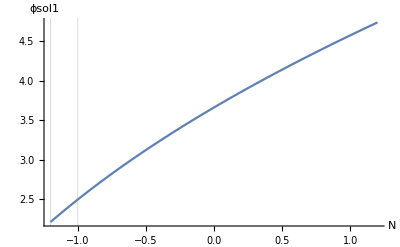

At n = 0, ϵ1 = 0.510894

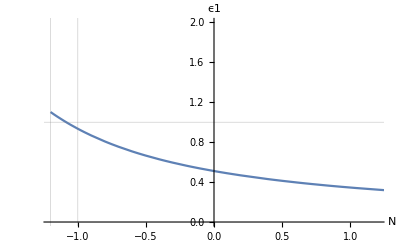

At n1 = -1.08469, ϵ1 = 1.

ϕi2 = 25.3095

ϕpi2 = 0.157789

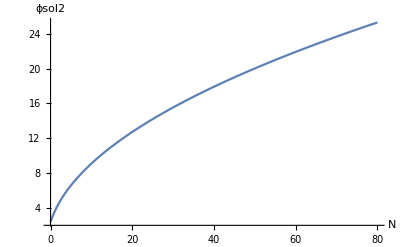

At n = 0, ϵ1 = 0.999988

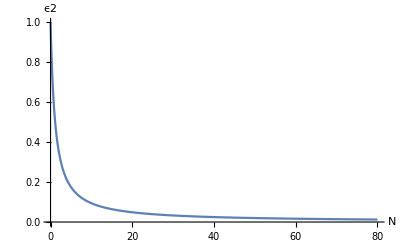

ns[60] = 0.950353

r[60] = 0.264982

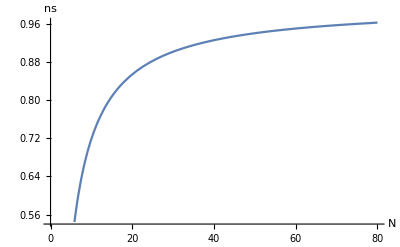

ϵsr[0] = 1.44996

ϵsr[60] = 0.0166532

ϵsrL[0] = 1.20414

ϵsrL[60] = 0.0166072

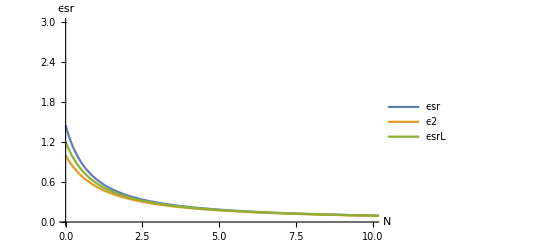

ηsr[0] = 2.21136

ηsr[60] = 0.0249756

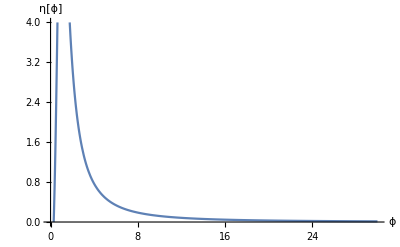

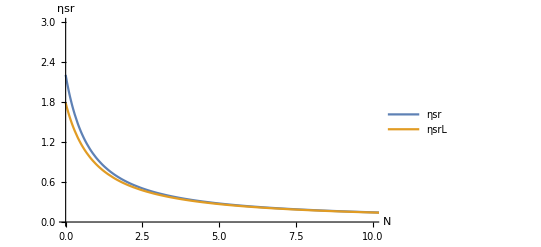

FindRoot::reged: The point {80.} is at the edge of the search region {0., 80.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

Zϵ = 0

Zη = 0

ns[60] = 0.950353 and r[60] = 0.264982

ns[50] = 0.940537 and r[50] = 0.317422

```mathematica
(* Define an inflationary potential *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(0.03)*x^4; *)
v[x_] := 1-1/2*x^2+(1)*x^4; 
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -1.2; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
{ns,r} = findNsR[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True]; (* Plots,Prints *)
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

0.35

FindRoot::reged: The point {80.} is at the edge of the search region {0., 80.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {x} = {0.1}.

ReplaceAll::reps: {FindRoot[ηsr$750039[x] == 0., {x, xInit, 0, 80}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {x} = {0.2}.

ReplaceAll::reps: {FindRoot[ηsr$750039[x] == 0., {x, xInit, 0, 80}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {x} = {0.3}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ηsr$750039[x] == 0., {x, xInit, 0, 80}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::srect: Value xInit in search specification {x, xInit, 0, 80} is not a number or array of numbers.

General::stop: Further output of FindRoot :: srect will be suppressed during this calculation.

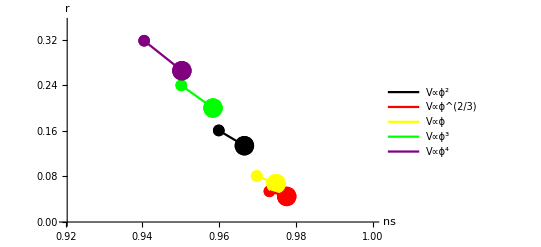

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 80; nf = -1.2; ni2 = 80; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35
Do[
Clear[v,vp,ns,r];
v[ϕ_] := ϕ^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
{ns,r} = findNsR[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```